```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,4,0.001]}]]
```

$Aborted

```mathematica
Pri[ω_]:=tr[ω,0.0001,1,0]
```

```mathematica
Clear[k14,k28,k42,k56,k84,k100,k114,k126,k7,k140,k21]
```

```mathematica
k14:=k14=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"]]
k28:=k28=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"]]
k42:=k42=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"]]
k56:=k56=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"]]
k70:=k70=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"]]
k84:=k84=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"]]
k100:=k100=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"]]
k114:=k114=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"]]
k126:=k126=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"]]
k140:=k140=Interpolation[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/140imp100.csv"]]
k7:=k7=Interpolation[Import["/home/shardulmukim/7imp100.dat"]]
k21:=k21=Interpolation[Import["/home/shardulmukim/21imp100.dat"]]
```

```mathematica
Clear[k7,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11]
```

```mathematica
k2:=k2=Table[{ω,k14[ω]},{ω,0,4,0.001}]
k3:=k3=Table[{ω,k28[ω]},{ω,0,4,0.001}]
k4:=k4=Table[{ω,k42[ω]},{ω,0,4,0.001}]
k5:=k5=Table[{ω,k56[ω]},{ω,0,4,0.001}]
k6:=k6=Table[{ω,k70[ω]},{ω,0,4,0.001}]
k7:=k7=Table[{ω,k84[ω]},{ω,0,4,0.001}]
k8:=k8=Table[{ω,k100[ω]},{ω,0,4,0.001}]
k9:=k9=Table[{ω,k114[ω]},{ω,0,4,0.001}]
k10:=k10=Table[{ω,k126[ω]},{ω,0,4,0.001}]
k11:=k11=Table[{ω,k140[ω]},{ω,0,4,0.001}]
```

```mathematica
f[ω_]:={{0,Pri[ω]},{1,k2[[ω*1000+1]][[2]]},{2,k3[[ω*1000+1]][[2]]},{3,k4[[ω*1000+1]][[2]]},{4,k5[[ω*1000+1]][[2]]},{5,k6[[ω*1000+1]][[2]]},{6,k7[[ω*1000+1]][[2]]},{7,k8[[ω*1000+1]][[2]]},{8,k9[[ω*1000+1]][[2]]},{9,k10[[ω*1000+1]][[2]]},{10,k11[[ω*1000+1]][[2]]}}
```

```mathematica
φ[ω_]:=Interpolation[f[ω]]
```

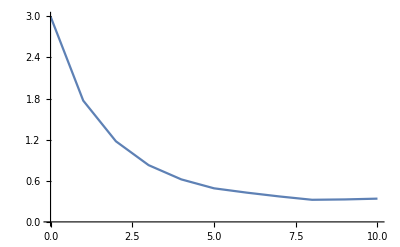

```mathematica
ListLinePlot[f[1.155]]
```

```mathematica
sloap[ω_,n_]:=(φ[ω][n]-φ[ω][n+.01])/0.01
```

```mathematica
Clear[s,γ]
```

```mathematica
s[ω_,l_]:=s[ω,l]=Mean[Table[sloap[ω,k],{k,Range[0,l,0.1]}]]
```

```mathematica
γ[ω_,n_]:=γ[ω,n]=(-2φ[ω][n]+φ[ω][n+.1]+φ[ω][n-.1])/(0.1)^2
```

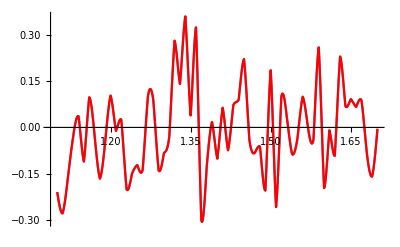

```mathematica
Show[ListLinePlot[Table[{ω,γ[ω,4]},{ω,Range[1.1,1.7,0.001]}],PlotRange->All],ListLinePlot[Table[{ω,γ[ω,4]},{ω,Range[1.1,1.7,0.001]}],PlotStyle->Red,PlotRange->All](*,ListLinePlot[Table[{ω,s[ω,9.99]},{ω,Range[0.0,2,0.01]}],PlotStyle->Red],PlotRange->All*)]
```

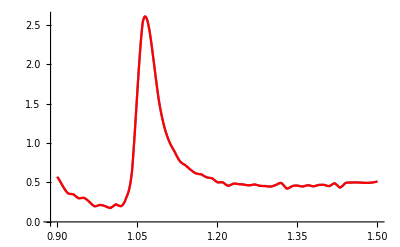

```mathematica
Show[ListLinePlot[Table[{ω,γ[ω,1]},{ω,Range[0.9,1.5,0.001]}],PlotRange->All],ListLinePlot[Table[{ω,γ[ω,1]},{ω,Range[0.9,1.5,0.001]}],PlotStyle->Red,PlotRange->All]]
```

```mathematica
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},7]
```

{imp6,imp11,imp4,imp14,imp8,imp9,imp7}

```mathematica
14*6+7
```

91

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},7],Table[imp,9]]]
```

{imp8,imp7,imp1,imp,imp4,imp5,imp1,imp4,imp11,imp6,imp4,imp10,imp3,imp7,imp9,imp6,imp10,imp11,imp11,imp10,imp6,imp,imp8,imp12,imp10,imp10,imp13,imp9,imp2,imp12,imp,imp12,imp14,imp9,imp2,imp11,imp6,imp,imp2,imp5,imp13,imp14,imp4,imp,imp8,imp5,imp10,imp7,imp,imp2,imp14,imp5,imp3,imp12,imp12,imp,imp11,imp5,imp11,imp9,imp2,imp3,imp,imp1,imp14,imp3,imp5,imp14,imp12,imp5,imp1,imp1,imp13,imp13,imp7,imp6,imp9,imp13,imp9,imp8,imp10,imp,imp4,imp14,imp3,imp6,imp4,imp3,imp7,imp6,imp8,imp2,imp4,imp13,imp8,imp14,imp8,imp2,imp7,imp1}

```mathematica
deltae[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp8,imp7,imp1,imp,imp4,imp5,imp1,imp4,imp11,imp6,imp4,imp10,imp3,imp7,imp9,imp6,imp10,imp11,imp11,imp10,imp6,imp,imp8,imp12,imp10,imp10,imp13,imp9,imp2,imp12,imp,imp12,imp14,imp9,imp2,imp11,imp6,imp,imp2,imp5,imp13,imp14,imp4,imp,imp8,imp5,imp10,imp7,imp,imp2,imp14,imp5,imp3,imp12,imp12,imp,imp11,imp5,imp11,imp9,imp2,imp3,imp,imp1,imp14,imp3,imp5,imp14,imp12,imp5,imp1,imp1,imp13,imp13,imp7,imp6,imp9,imp13,imp9,imp8,imp10,imp,imp4,imp14,imp3,imp6,imp4,imp3,imp7,imp6,imp8,imp2,imp4,imp13,imp8,imp14,imp8,imp2,imp7,imp1}};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
Table[{ω,If[tra>3,3,tra]},{ω,Range[0,3,0.01]}]]
```

```mathematica
aa=Table[deltae[0.5],50]
```

{{{0.,0.0000495488},{0.01,0.0000171091},{0.02,6.80977×10^-6},{0.03,0.0000177002},{0.04,0.0000495678},{0.05,0.000102926},{0.06,0.000179049},{0.07,0.000280067},{0.08,0.000409116},{0.09,0.000570585},{0.1,0.000770484},{0.11,0.00101699},{0.12,0.00132125},276,{2.89,0.0795649},{2.9,0.0433999},{2.91,0.0278957},{2.92,0.0195166},{2.93,0.0143964},{2.94,0.0110157},{2.95,0.00866046},{2.96,0.00695328},{2.97,0.00567747},{2.98,0.0047005},{2.99,0.00393731},{3.,0.00333109}},48,{1}}
 |  |  |  |

```mathematica
pp=Table[Table[{ω,Interpolation[aa[[δ]]][ω]},{ω,0,3,0.001}],{δ,50}]
```

{{{0.,0.0000495488},{0.001,0.0000452814},{0.002,0.000041244},{0.003,0.0000374356},{0.004,0.0000338552},{0.005,0.000030502},{0.006,0.0000273749},{0.007,0.000024473},{0.008,0.0000217954},{0.009,0.0000193411},{0.01,0.0000171091},{0.011,0.0000150985},2978,{2.99,0.00393731},{2.991,0.00387056},{2.992,0.00380533},{2.993,0.00374155},{2.994,0.00367917},{2.995,0.00361813},{2.996,0.00355838},{2.997,0.00349985},{2.998,0.0034425},{2.999,0.00338627},{3.,0.00333109}},48,{1}}
 |  |  |  |

```mathematica
ns[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,k]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,k]*s[ω,k]+0*Abs[γ[ω,k]]*(Pri[ω]-pp[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
nss[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,0]*(Pri[ω]-%935[[δ]][[ω*1000+1]][[2]])},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,0]*s[ω,0]+2*γ[ω,k]*(Pri[ω]-%935[[δ]][[ω*1000+1]][[2]]))},{ω,Range[lim1,lim2,0.001]}]][ω],{ω,lim1,lim2}])
```

```mathematica
Table[ns[0.7,1.5,δ,7],{δ,50}]
```

{6.81413,6.70365,6.86608,6.83164,6.63478,6.71345,6.53945,6.7072,6.36736,6.72547,6.74323,6.91251,7.11474,7.00563,6.56184,6.83064,6.72965,6.97562,6.49045,6.6582,6.78789,6.67533,6.57013,6.77756,6.80154,6.82317,6.59547,6.87991,6.5695,6.66951,6.64907,6.54889,6.19699,6.31086,6.5208,6.62282,6.97619,6.62881,6.50064,6.81554,6.48679,6.7034,6.68024,6.72772,6.57503,6.61182,6.53318,6.78383,6.75969,6.69731}

```mathematica
Around[%953]
```

4.410.13

```mathematica
Around[%941]
```

0.550.04

```mathematica
Table[{k,nss[1.1,1.5,17,k]},{k,Range[0.5,8,0.5]}]
```

{{0.5,0.593661},{1.,0.685431},{1.5,0.810761},{2.,2.18831},{2.5,1.05341},{3.,1.21244},{3.5,1.17357},{4.,1.41458},{4.5,1.23888},{5.,1.16276},{5.5,1.28762},{6.,1.51706},{6.5,1.32207},{7.,1.29839},{7.5,1.3133},{8.,1.23288}}

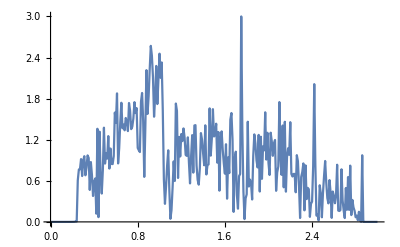

```mathematica
ListLinePlot[deltae[0.5]]
```

```mathematica
Clear[deltae2]
```

```mathematica
deltae2[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp,imp9,imp,imp3,imp,imp10,imp,imp,imp3,imp12,imp6,imp4,imp,imp,imp6,imp,imp,imp13,imp,imp7,imp8,imp1,imp,imp,imp12,imp,imp,imp,imp,imp,imp,imp,imp7,imp4,imp,imp1,imp,imp8,imp,imp11,imp,imp14,imp,imp,imp,imp,imp,imp2,imp2,imp,imp,imp9,imp14,imp,imp,imp,imp,imp,imp2,imp,imp13,imp11,imp,imp,imp3,imp,imp14,imp,imp5,imp13,imp4,imp,imp,imp6,imp,imp,imp,imp7,imp10,imp,imp9,imp,imp,imp10,imp,imp5,imp,imp,imp,imp5,imp8,imp12,imp,imp,imp,imp11,imp,imp,imp1,imp}};b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
Table[{ω,If[tra>3,3,tra]},{ω,Range[0,3,0.01]}]]
```

```mathematica
deltae3[ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp7,imp12,imp10,imp,imp14,imp13,imp9,imp3,imp,imp11,imp12,imp2,imp9,imp4,imp6,imp4,imp,imp2,imp14,imp,imp13,imp7,imp,imp13,imp1,imp,imp,imp7,imp12,imp9,imp9,imp4,imp1,imp2,imp14,imp9,imp7,imp5,imp10,imp,imp2,imp6,imp1,imp8,imp11,imp3,imp13,imp3,imp7,imp10,imp6,imp13,imp,imp,imp5,imp10,imp2,imp3,imp12,imp3,imp13,imp5,imp14,imp10,imp8,imp6,imp3,imp7,imp11,imp,imp4,imp11,imp,imp12,imp11,imp12,imp5,imp1,imp10,imp2,imp9,imp5,imp,imp6,imp11,imp,imp,imp5,imp8,imp1,imp4,imp14,imp1,imp8,imp4,imp14,imp8,imp8,imp6,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
Table[{ω,tra},{ω,Range[0,4,0.01]}]]
```

```mathematica
Table[deltae2[0.5],50]
```

{{{0.,2.20837×10^-7},{0.01,9.23639×10^-6},{0.02,7.50177×10^-7},{0.03,6.41426×10^-6},{0.04,2.04391×10^-7},{0.05,0.000124954},{0.06,3.01539×10^-7},{0.07,0.000355805},{0.08,0.000398687},{0.09,0.000504825},{0.1,1.86306×10^-6},{0.11,0.000317222},277,{2.89,0.156513},{2.9,0.000715094},{2.91,0.00544472},{2.92,0.0000648615},{2.93,0.0000776751},{2.94,3.04974×10^-7},{2.95,0.0000173001},{2.96,0.0000207329},{2.97,1.59729×10^-7},{2.98,4.81251×10^-6},{2.99,0.000512824},{3.,4.31366×10^-7}},48,{1}}
 |  |  |  |

```mathematica
intg2[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,0]*(tr[ω,0.0001,1,0]-%725[[δ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,0]*s[ω,0]+2*γ[ω,k]*(tr[ω,0.0001,1,0]-%725[[δ]][[ω*100+1]][[2]]))},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}])
```

```mathematica
intg1[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,s[ω,k]*(tr[ω,0.0001,1,0]-%725[[δ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(s[ω,k]*s[ω,k]+0*γ[ω,k]*(tr[ω,0.0001,1,0]-%725[[δ]][[ω*100+1]][[2]]))},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}])
```

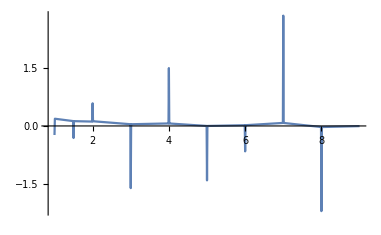

```mathematica
ListLinePlot[Table[{n,γ[1.95,n]},{n,Range[1,9,.01]}],PlotRange->All]
```

```mathematica
Table[{k,Around[Table[Abs[intg1[0.9,1.5,y,k]],{y,50}]],Around[Table[Abs[intg2[0.9,1.5,y,k]],{y,50}]]},{k,0.5,8,0.5}]
```

{{0.5,1.2620.027,0.4060.004},{1.,1.750.04,0.4370.018},{1.5,2.180.05,5.31.2},{2.,2.570.05,4.00.8},{2.5,2.940.06,0.7620.015},{3.,3.290.07,0.960.04},{3.5,3.650.08,0.8010.017},{4.,4.000.08,2.500.26},{4.5,4.350.09,0.8230.017},{5.,4.700.10,0.6060.014},{5.5,5.060.11,0.8380.018},{6.,5.420.11,1.420.07},{6.5,5.780.12,0.8520.019},{7.,6.130.13,1.570.16},{7.5,6.470.14,0.8450.018},{8.,6.820.14,0.4690.017}}

```mathematica
Table[{k,Around[Table[Abs[intg1[0.9,1.5,y,k]],{y,50}]],Around[Table[Abs[intg2[0.9,1.5,y,k]],{y,50}]]},{k,5,8,1}]
```

{{5,5.180.10,0.6300.013},{6,5.990.11,1.620.08},{7,6.780.13,2.040.23},{8,7.550.14,0.4660.014}}

```mathematica
Around[%692]
```

2.50.5

```mathematica
Around[%309]
```

0.020.04

```mathematica
Around[%277]
```

-0.0060.035

```mathematica
Around[%273]
```

1.0100.033

```mathematica
Around[%258]
```

1.0130.033

```mathematica
Around[%251]
```

7.000.11

```mathematica
Around[%243]
```

5.990.13

```mathematica
Around[%232]
```

4.980.09

```mathematica
Around[%195]
```

3.000.07

```mathematica
Around[%156]
```

2.000.06

```mathematica
Mean[%78]
```

6.01534

```mathematica
Table[Around[Table[(%210[[x]][[y]]),{x,100}]],{y,10}]
```

{0.9110.034,0.830.05,0.630.06,0.430.08,0.200.09,0.080.07,0.200.10,0.420.13,0.560.15,0.690.16}

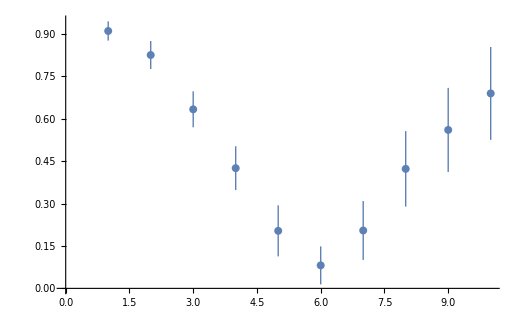

```mathematica
ListPlot[%218]
```

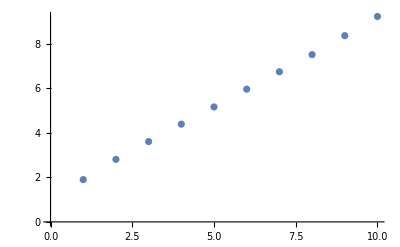

```mathematica
ListPlot[{1.899110347123335,2.807057700141082,3.6069593277769028,4.390499078346073,5.161775723538891,5.959830714949398,6.744569518702641,7.5121026720106405,8.364202046198988,9.226572901743994}]
```

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{6.12555,6.26514,5.92818,6.03313,5.95201,6.03502,6.06434,5.82361,6.23969,6.10335,6.07553,6.03243,6.16288,6.06536,5.99633,6.00033,6.11281,6.02479,6.00611,5.85925,5.8461,5.88507,6.01672,5.84072,6.01959,6.00502,6.11205,6.01062,6.06377,5.95565,6.09998,6.29698,5.83896,6.03958,6.03951,5.94342,5.9727,6.01477,5.91905,5.9769,5.998,5.98179,5.75244,5.88456,6.02668,5.95983,6.01148,5.94988,6.09948,5.88714,6.01575,5.92145,5.92397,5.93783,5.97937,5.99439,6.13902,5.95961,6.08194,6.00151,5.84119,6.07206,6.03414,5.91467,6.1563,6.06842,6.07152,5.89674,6.08445,6.00792,5.78854,5.92672,6.0432,6.07062,5.97701,5.92096,5.91498,5.95779,5.91103,5.84623,6.14261,5.97987,6.08964,6.10847,5.99127,5.98823,5.83923,6.14637,6.08906,5.9393,6.13106,6.03914,6.23913,5.9436,6.2493,6.00122,6.17588,6.02124,6.08132,6.0237}

```mathematica
Export["6imppoi.dat",%146]
```

6imppoi.dat

```mathematica
Around[%146]
```

6.010.11

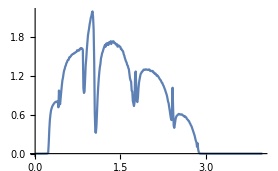

```mathematica
ListLinePlot[Import["21imp100.dat"]]
```

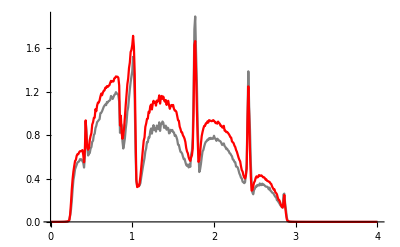

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"],PlotStyle->Gray],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"],PlotStyle->Red],PlotRange->All]
```

```mathematica
intg2[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,Mean[s[ω,k]]*(tr[ω,0.0001,1,0]-%93[[δ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/(NIntegrate[Interpolation[Table[{ω,(Mean[s[ω,k]]*Mean[s[ω,k]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}])
```

```mathematica
Misfit[lim1_,lim2_,δ_,k_]:=NIntegrate[Interpolation[Table[{ω,(tr[ω,0.0001,1,0]-%602[[δ]][[ω*100+1]][[2]])^2},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}](*-2*k*NIntegrate[Interpolation[Table[{ω,Mean[s[ω,k]]*(tr[ω,0.0001,1,0]-%602[[δ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/100*)
```

```mathematica
Misfit[0.9,1.5,2,3]
```

2.48951

```mathematica
Table[Table[Misfit[0.9,1.5,δ,k],{k,Range[1,8,1]}],{δ,100}]
```

{{2.48754,2.4753,2.46793,2.46325,2.45994,2.45782,2.45614,2.45477},{2.46131,2.44911,2.44176,2.43708,2.4338,2.43171,2.43004,2.42869},{2.51676,2.50439,2.49694,2.49219,2.48883,2.48669,2.48499,2.48358},{2.29715,2.28544,2.27839,2.27389,2.27075,2.26872,2.26711,2.26576},{2.50713,2.49471,2.4872,2.48242,2.47905,2.47689,2.47517,2.47375},{2.33567,2.32381,2.31667,2.31214,2.30893,2.30689,2.30527,2.30394},{2.37561,2.36364,2.35641,2.35178,2.34854,2.34647,2.34481,2.34347},{2.60813,2.59543,2.58776,2.58285,2.57938,2.57715,2.57535,2.5738},{2.7823,2.76925,2.76134,2.75632,2.7528,2.75057,2.74878,2.74729},{2.62112,2.60843,2.60075,2.59588,2.59245,2.59027,2.58854,2.58708},{2.52923,2.5167,2.50911,2.50427,2.50087,2.49869,2.49697,2.49558},{2.43626,2.42401,2.41661,2.4119,2.40859,2.40648,2.40481,2.40344},{2.49796,2.48562,2.47818,2.47347,2.47015,2.46806,2.46638,2.46497},{2.56421,2.55175,2.54424,2.53945,2.53612,2.53399,2.5323,2.53092},{2.28122,2.26949,2.26242,2.25793,2.25477,2.25275,2.25113,2.24977},{2.43364,2.42145,2.41413,2.4095,2.40626,2.40421,2.40258,2.40125},{2.43382,2.42167,2.4143,2.40962,2.40631,2.40421,2.40253,2.40115},{2.53414,2.52176,2.51427,2.50947,2.50612,2.50396,2.50225,2.50082},{2.55427,2.54183,2.53432,2.52951,2.52613,2.52397,2.52225,2.52082},{2.76898,2.75591,2.748,2.74297,2.73943,2.73718,2.73538,2.7339},{2.49478,2.48245,2.47501,2.47032,2.46703,2.46496,2.46332,2.46201},{2.43644,2.42427,2.41695,2.41231,2.40903,2.40695,2.4053,2.40396},{2.41993,2.40793,2.4007,2.39612,2.39292,2.39089,2.38928,2.38794},{2.41038,2.3983,2.39105,2.38648,2.38324,2.3812,2.37958,2.37825},{2.46081,2.44858,2.4412,2.43647,2.43313,2.43098,2.42927,2.42781},{2.47245,2.46019,2.45278,2.44807,2.44476,2.44265,2.44097,2.43958},{2.32501,2.31315,2.30604,2.30156,2.29841,2.29643,2.29486,2.29361},{2.17595,2.16456,2.15772,2.15339,2.15035,2.14841,2.14687,2.14554},{2.46455,2.45221,2.44476,2.44005,2.43675,2.43464,2.43298,2.43163},{2.4581,2.44585,2.43848,2.43379,2.43048,2.42837,2.42669,2.42528},{2.70039,2.6877,2.68006,2.67518,2.67176,2.66959,2.66787,2.6665},{2.47606,2.46392,2.45663,2.45201,2.44874,2.44666,2.44501,2.44363},{2.46454,2.45223,2.44483,2.44013,2.43684,2.43476,2.43311,2.43179},{2.63171,2.61914,2.61154,2.60671,2.6033,2.60109,2.59937,2.59793},{2.37767,2.36556,2.35824,2.35359,2.35031,2.34822,2.34656,2.3452},{2.38073,2.36869,2.36146,2.35688,2.35366,2.35162,2.35,2.34866},{2.45359,2.44136,2.434,2.42933,2.42604,2.42396,2.4223,2.42093},{2.25809,2.24632,2.23923,2.23474,2.23156,2.22955,2.22794,2.2266},{2.40781,2.39573,2.38844,2.3838,2.38054,2.37848,2.37683,2.37549},{2.54198,2.52947,2.52189,2.51704,2.51364,2.51147,2.50973,2.50832},{2.45083,2.43855,2.43112,2.42637,2.42303,2.42088,2.41916,2.41773},{2.57213,2.55961,2.55207,2.54731,2.54395,2.54186,2.5402,2.53888},{2.71459,2.7018,2.69413,2.68928,2.68588,2.68373,2.68203,2.68065},{2.34674,2.33469,2.3274,2.32276,2.31948,2.3174,2.31574,2.31438},{2.35555,2.34369,2.33649,2.33188,2.32861,2.3265,2.32479,2.32334},{2.29249,2.28072,2.27365,2.26917,2.266,2.26399,2.2624,2.26109},{2.35031,2.33829,2.33102,2.3264,2.32314,2.32106,2.31939,2.31801},{2.31177,2.29999,2.29292,2.2884,2.28521,2.28317,2.28153,2.2802},{2.37348,2.36148,2.35424,2.34963,2.34641,2.34434,2.3427,2.34134},{2.40829,2.39625,2.38902,2.38445,2.38123,2.3792,2.37758,2.3763},{2.43727,2.42513,2.41785,2.41325,2.41001,2.40795,2.40632,2.405},{2.46258,2.45036,2.443,2.43834,2.43507,2.43299,2.43135,2.43005},{2.43356,2.42139,2.41402,2.40935,2.40606,2.40396,2.40229,2.40093},{2.5102,2.49782,2.49038,2.48567,2.48235,2.48025,2.47858,2.47723},{2.28719,2.27539,2.26828,2.26376,2.26057,2.25857,2.25696,2.25562},{2.59054,2.57798,2.57044,2.56568,2.56231,2.5602,2.55852,2.55714},{2.5024,2.4901,2.48273,2.47807,2.47479,2.47273,2.47109,2.46975},{2.36394,2.35199,2.34478,2.34023,2.33701,2.33496,2.33333,2.33198},{2.42313,2.41111,2.40392,2.39939,2.39621,2.39421,2.39261,2.39134},{2.36184,2.34986,2.34266,2.33811,2.33489,2.33285,2.33123,2.32988},{2.6393,2.62657,2.6189,2.61404,2.61061,2.60844,2.60672,2.60528},{2.55834,2.54585,2.53831,2.5335,2.53012,2.52795,2.52623,2.5248},{2.31472,2.3028,2.2956,2.29103,2.2878,2.28574,2.28409,2.28273},{2.42313,2.41113,2.4039,2.39933,2.39613,2.39412,2.39252,2.39125},{2.35681,2.34489,2.33774,2.33321,2.33001,2.32798,2.32638,2.32506},{2.26625,2.25462,2.24761,2.24317,2.24005,2.23807,2.2365,2.23521},{2.31679,2.30497,2.29786,2.29333,2.29015,2.28812,2.28651,2.28518},{2.42226,2.41018,2.40297,2.39841,2.39518,2.39315,2.39154,2.39023},{2.64294,2.63015,2.62242,2.6175,2.61402,2.61182,2.61006,2.60858},{2.57501,2.56249,2.55497,2.55023,2.54688,2.54475,2.54307,2.54169},{2.52073,2.5084,2.50099,2.49634,2.49308,2.49104,2.48943,2.48815},{2.30665,2.29482,2.28768,2.28315,2.27996,2.2779,2.27626,2.27484},{2.45452,2.44229,2.43491,2.43022,2.42695,2.42484,2.42318,2.42185},{2.34432,2.33251,2.32541,2.32089,2.31768,2.31565,2.31403,2.31267},{2.5063,2.4941,2.48676,2.48212,2.47887,2.47681,2.47518,2.47382},{2.50651,2.49424,2.48683,2.48212,2.4788,2.47669,2.47501,2.47363},{2.1997,2.18812,2.18114,2.17669,2.17354,2.17153,2.16991,2.16858},{2.65129,2.63853,2.63083,2.62593,2.62249,2.6203,2.61856,2.61716},{2.11881,2.10756,2.1008,2.09653,2.09354,2.09165,2.09015,2.08895},{2.53403,2.52161,2.51411,2.50937,2.50603,2.50393,2.50227,2.50091},{2.55416,2.54166,2.53413,2.52934,2.52597,2.52382,2.52212,2.52069},{2.25682,2.24514,2.23806,2.23357,2.23042,2.22841,2.22681,2.2255},{2.26655,2.25488,2.24788,2.24344,2.24031,2.23832,2.23672,2.23537},{2.42578,2.41361,2.40629,2.40166,2.39839,2.39632,2.39467,2.3933},{2.64163,2.6289,2.6212,2.6163,2.61284,2.61063,2.60887,2.60739},{2.41394,2.40186,2.39457,2.38996,2.38671,2.38465,2.38301,2.38168},{2.35234,2.34047,2.33336,2.3289,2.32574,2.32377,2.3222,2.32093},{2.63502,2.62237,2.61475,2.60991,2.60651,2.60435,2.60264,2.60122},{2.71133,2.69844,2.69067,2.68571,2.68221,2.67998,2.67819,2.67669},{2.37966,2.36761,2.36037,2.35579,2.35258,2.35055,2.34895,2.34768},{2.30604,2.29417,2.28697,2.28237,2.27912,2.27702,2.27534,2.27385},{2.23722,2.22566,2.21874,2.2144,2.21132,2.20938,2.20783,2.20652},{2.49185,2.47959,2.47223,2.46752,2.46422,2.46211,2.46042,2.45902},{2.41901,2.40699,2.39976,2.39519,2.39198,2.38998,2.38839,2.3871},{2.62699,2.61438,2.60677,2.60192,2.59852,2.59635,2.5946,2.59313},{2.50441,2.49202,2.48457,2.47984,2.47652,2.47441,2.47276,2.47142},{2.44258,2.4305,2.42324,2.41864,2.4154,2.41334,2.4117,2.41039},{2.30057,2.28873,2.2816,2.27706,2.27386,2.27181,2.27018,2.2688},{2.47878,2.46652,2.45913,2.45442,2.45111,2.44901,2.44733,2.44598},{2.29174,2.27998,2.27291,2.2684,2.26524,2.26322,2.26161,2.26031}}

```mathematica
Table[Around[Table[%604[[x]][[y]],{x,100}]],{y,8}]
```

{2.450.13,2.440.13,2.430.13,2.420.13,2.420.13,2.420.13,2.420.13,2.420.13}